```mathematica
n=23;
(*s=0.3;*)
σ=0.3;
e=Exp[σ^2/2];

a=Table[0,{i,n}];b=a;
a[[1]]=e;
b[[1]]=0;
Do[
	a[[j+1]]=((e^2+1)e^(2 j)-1)e^(2j-1);
	b[[j+1]]=(e^(2 j)-1)e^(6 j-4);
,{j,1,n-1}];

Ja=DiagonalMatrix[a];
Do[
Ja[[i,i+1]]=b[[i+1]]//Sqrt;
Ja[[i+1,i]]=b[[i+1]]//Sqrt;
,{i,n-1}];

esys=Eigensystem[Ja];
eval=esys[[1]]
evec=esys[[2]];
w=Table[evec[[i,1]]^2,{i,1,n}]//Abs
```

{144.649,99.0705,72.0246,53.9412,41.1438,31.7732,24.7531,19.4067,15.2846,12.0762,9.56045,7.57611,6.00364,4.75293,3.75525,2.95762,2.3188,1.80647,1.39505,1.06407,0.796915,0.57936,0.396804}

{1.14843×10^-60,0.,0.,0.,5.24156×10^-34,4.6392×10^-30,4.67847×10^-26,1.93022×10^-22,3.61467×10^-19,3.30845×10^-16,1.56134×10^-13,3.94815×10^-11,5.49456×10^-9,4.28014×10^-7,0.000018811,0.000465924,0.00643155,0.0483179,0.189581,0.362746,0.300916,0.0865186,0.00500323}

```mathematica
𝒟ro=LogNormalDistribution[0,σ];
momRo[i_]:=Moment[𝒟ro,i];
momRos=Table[momRo[i],{i,0,2n-1}];
{Ros,wRos}=wheeler[momRos];
```

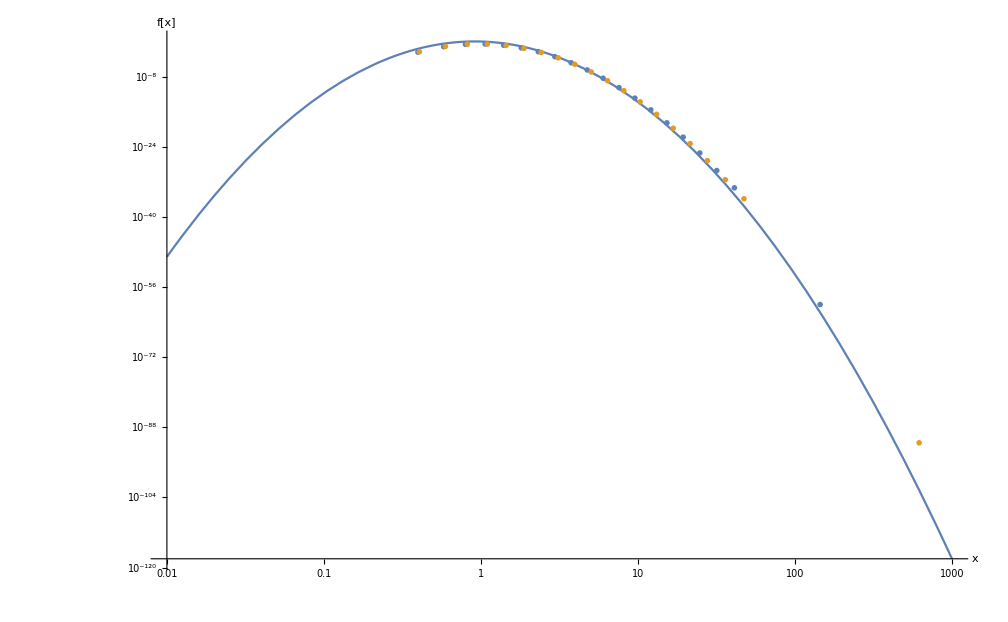

```mathematica
Show[
LogLogPlot[PDF[LogNormalDistribution[0,σ],x],{x,0.01,1000},PlotRange->All,AxesLabel->{"x","f[x]"}],
ListLogLogPlot[{Thread[{eval,w}],Thread[{Ros,wRos}]},PlotRange->All,PlotMarkers->{"OpenMarkers",10},AxesLabel->{"x","f[x]"}]
]
```

```mathematica
w
```

{3.44881×10^-166,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.94659×10^-36,2.33553×10^-33,6.10668×10^-30,1.03425×10^-26,1.14167×10^-23,8.25118×10^-21,3.91565×10^-18,1.22163×10^-15,2.50446×10^-13,3.36584×10^-11,2.95209×10^-9,1.67797×10^-7,6.11921×10^-6,0.000141198,0.0020227,0.0175269,0.0886028,0.24813,0.356175,0.231084,0.0537393,0.00257184}

```mathematica
eval
```

{3.6627,2.29081,1.4993,0.981271,0.613729}